## Constants, Units and Parameters

```mathematica
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"];
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9;THz=10^12;
m=1;cm=10^-2;mm=10^-3;μm=10^-6;nm=10^-9;pm=10^-12;
s=1;ms=10^-3;μs=10^-6;ns=10^-9;ps=10^-12;
Gauss=10^-4;mG=10^-3 Gauss;μG=10^-6 Gauss;T=1;
mW=10^-3;μW=10^-6;
c=2.99792458 10^8 m/s;
μ0=4π 10^-7;
ϵ0=1/(μ0 c^2);
h=6.62606896 10^-34;
ℏ=h/(2π);
e=1.602176487 10^-19;
μB=9.27400915 10^-24;
AMU=1.660538782 10^-27;
AME=9.10938215 10^-31;
a0=0.52917720859 10^-10 m;
kB=1.3806504 10^-23;
Kelvin=1;μK=10^-6 Kelvin;nK=10^-9 Kelvin;

AbundanceK39=93.2581 0.01;
AbundanceK40=0.0117 0.01;
AbundanceK41=6.7302 0.01;
massK39=38.96370668AMU;
massK40=39.96399848AMU;
massK41=40.96182576 AMU;
Meltingpoint=336.8K;
Boilingpoint=1047.15K;

λD1K40=770.108136507nm;
ΓD1K40=2π 5.956MHz;
ωD1K40=c/λD1K40 2π;
λD2K40=766.700674872nm;
ΓD2K40=2π 6.035MHz;
ωD2K40=c/λD2K40 2π;

AhfGroundK40=-285.7308MHz;
AhfD1K40=-34.523MHz;
AhfD2K40=-7.585MHz;
BhfD2K40=-3.445MHz;
gs=2.0023193043622;
gIK40=0.000176490;
gJGround=2.00229421;
gJD1=2./3;
gJD2=4./3;

λtrap=1053.57nm;
ωtrap=c/λtrap 2π;
λlat=λtrap;
ωlat=ωtrap;
klat=(2π)/λlat;
Erecoil=(ℏ^2 klat^2)/(2 massK40);
```

## lattice parameters

```mathematica
(*Lattice parameters*)
```

```mathematica
Vlatx=2.5;(*unit: Er*)
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;

(*angles*)
(*-Graphics-*)
θxdt1=57.15/180 π;θxdt2=29.24/180 π;θxlat=30.17/180 π;θylat=31.54/180 π;
vecxdt1=({{Cos[θxdt1]}, {-Sin[θxdt1]}});vecxlat=({{Sin[θxlat]}, {Cos[θxlat]}});vecylat=({{Cos[θylat]}, {-Sin[θylat]}});
Clear[hh,kk];
solangle=Solve[hh+kk*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])==Cos[θxdt1]*Sin[θxlat]-Sin[θxdt1]Cos[θxlat]&&
hh*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])+kk==Cos[θxdt1]*Cos[θylat]+Sin[θxdt1]Sin[θylat],{hh,kk}]
xdt1toxlat=solangle⟦1,1,2⟧
xdt1toylat=solangle⟦1,2,2⟧
```

{{hh→-0.432367,kk→0.89142}}

-0.432367

0.89142

### do not project along one lattice direction. Assumption : isotropic cubic lattice

```mathematica
xdt1toxlat=1;
xdt1toylat=0;
```

## overall trap frequency (including harmonic confinement of lattice beams)

```mathematica
λlat=1054nm;
klat=(2π)/λlat;
Er=(ℏ^2 klat^2)/(2 massK40);
w0x=60μm;
w0y=60μm;
w0z=85μm;

xdt1=0.15;
xdtfreq=√(xdt1*1000)*3.29116-15.03525
xdtfreq=32;


fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π)
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
f0= √(1*xdtfreq^2+fx^2)
```

25.2731

56.8725

56.8725

65.7086

65.257

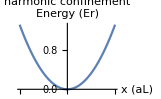

```mathematica
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Plot[potential[x,f0],{x,-50,50},PlotLabel->"harmonic confinement",AxesLabel->{"x (aL)","Energy (Er)"}]
```

```mathematica
onsiteU=0.407634 h kHz/Erecoil (174(1-7.5/(20-202.1)))/174 
tunnelling= 0.12642;(*unit is Erecoil*)
(*tempβ=4;*)
(*1/(kB Temp) = 1/Er*)
```

0.0943664

```mathematica
0.577687 h kHz/Erecoil(174(1-7.5/(20-202.1)))/174
```

0.133733

```mathematica
0.12642
```

0.12642

```mathematica
0.0943664
```

0.0943664

```mathematica
2.43759 h kHz/Erecoil (174(1-7.5/(20-202.1)))/174
```

0.564297

## manipulate folder list && calculate(1Er,t=0.178514,U=)

```mathematica
folderls={"20G",         "180G",     "197.5G","200G",     "201G",  "205G",       "206G",          "207G",          "210G",          "222Er",       "333Er",       "444Er",      "3.5Er",       "111Er",  "198G",   "199p5G",   "200p5G","15Er","555Er-200G"};
ttls=         {0.000001,     0.12642,  0.12642,   0.12642,   0.12642,0.12642,    0.12642,        0.12642, 0.12642,  0.14305,   0.111252,    0.0856614,  0.0976734,   0.178514,  0.12642,   0.12642,   0.12642,0.00653173, 0.0658986};
UUls=         {1.00001,0.121392,0.238406,0.414325, 0.70859,-0.143764, -0.0836618,-0.0480913, 0.00458904, 0.0758841, 0.113742,     0.154097,    0.133733,    0.0426963,    0.256427,   0.350277,  0.515478, 0.56297, 0.857072};
```

```mathematica
For[iifolder=19,iifolder≤ 19,iifolder++,
{
pathexp=StringJoin["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/","cubic-results-",folderls⟦iifolder⟧];
ttvalue=ttls⟦iifolder⟧;
UUvalue=UUls⟦iifolder⟧;
Print[StringJoin[ToString[folderls⟦iifolder⟧],"; t=",ToString[ttvalue],";U=",ToString[UUvalue]]];

calcedpath=StringJoin[pathexp,"/yes.txt"];
calcedcheck=Check[Import[calcedpath];True,False];
If[calcedcheck,
{
Print["calculated!"]
},
{
Print["start to calculate!"];
If[Length[StringCases[folderls⟦iifolder⟧,x_~~"G"-> x]]≥ 1,
{
Print["B field data sets"]
},
{
Print["lat depth data sets"];
(*trap freq*);
Vlatx=15;ToExpression[StringCases[folderls⟦iifolder⟧,x_~~"Er"-> x]⟦1⟧];(*unit: Er*);
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;
fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π);
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π);
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π);
f0= √(1*xdtfreq^2+fx^2);
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Print["vlat=",ToString[Vlatx],";    f0=",ToString[f0]];
(*end of trap freq & potential*);
}
];

(*write geom file*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
tJold=ww⟦35⟧; 
onsiteUold=ww⟦60⟧;
tJnew=ttvalue;
onsiteUnew=UUvalue;
wwtJold1=StringJoin["0 0 1.0 0.0 0.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwtJold2=StringJoin["0 0 0.0 1.0 0.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwtJold3=StringJoin["0 0 0.0 0.0 1.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwUold=     StringJoin["0 0 0.0 0.0 0.0 0.0 0.0 ",ToString[onsiteUold]];

wwtJnew1=StringJoin["0 0 1.0 0.0 0.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwtJnew2=StringJoin["0 0 0.0 1.0 0.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwtJnew3=StringJoin["0 0 0.0 0.0 1.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwUnew=     StringJoin["0 0 0.0 0.0 0.0 0.0 0.0 ",ToString[onsiteUnew]];

writenew=StringReplace[writetemp,{wwtJold1-> wwtJnew1,wwtJold2-> wwtJnew2,wwtJold3-> wwtJnew3,wwUold-> wwUnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom",writenew,"Text"];
(*end of write geom file*);

(*start MC simulation*);

Run["clear"];

iitempstart=0.5001;iitempend=0.5002;δiitemp=0.041;
iiμstart=-0.5001;iiμend=-0.5001;δμ=0.0802;
(*save readme files*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
Export[StringJoin[pathexp,"/readme_in"],write,"Text"];

write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
Export[StringJoin[pathexp,"/readme_cubic.geom"],write,"Text"];
paralist={0,0};
paralist⟦1⟧={"iitempstart","iitempend","δiitemp","iiμstart","iiμend","δμ","onsiteU","tunnelling"};
paralist⟦2⟧={iitempstart,iitempend,δiitemp,iiμstart,iiμend,δμ,onsiteUnew,tJnew};
Export[StringJoin[pathexp,"/readme_paralist.txt"],paralist,"TSV"];

(*end save readme files*);
outputstring={"tempβ","μ","density","err","doublon","err","int_energy","err","kinetic_energy","err","total_energy","err"};
calcoutput={outputstring};
For[iitemp=iitempstart,iitemp≤ iitempend,iitemp=iitemp+δiitemp,
{
Print[Now];
iitempβ=1/iitemp;
Ltemp=50;
dtempβ=iitempβ/Ltemp;
Print[dtempβ];
Print["==========================================================="];
(*write the tempβ, into the in file for calculation*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwdτ=ww⟦Position[ww,"dtau"]⟦1,1⟧+1⟧;
wwL=ww⟦Position[ww,"L"]⟦1,1⟧+1⟧;

wwdτold=StringJoin["dtau   =  ",ToString[wwdτ]];
wwLold=  StringJoin["L      =  ",ToString[wwL]];

wwdτnew=StringJoin["dtau   =  ",ToString[dtempβ]];
wwLnew=  StringJoin["L      =  ",ToString[Ltemp]];

writenew=StringReplace[writetemp,{wwLold-> wwLnew,wwdτold-> wwdτnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*end of ..........*)(*write the tempβ, into the in file for calculation*);

For[iiμ=iiμstart,iiμ≤ iiμend,iiμ=iiμ+δμ,
{
If[Abs[iiμ]<0.00001,iiμ=0];
(*write the chemical potential μ into the in file for calculation*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwμup=ww⟦Position[ww,"up"]⟦1,1⟧+1⟧;
wwμdn=ww⟦Position[ww,"dn"]⟦1,1⟧+1⟧;

wwμupold=StringJoin["mu_up  =  ",ToString[wwμup]];
wwμdnold=StringJoin["mu_dn  =  ",ToString[wwμdn]];

wwμupnew=StringJoin["mu_up  =  ",ToString[iiμ]];
wwμdnnew=StringJoin["mu_dn  =  ",ToString[iiμ]];

writenew=StringReplace[writetemp,{wwμupold-> wwμupnew,wwμdnold-> wwμdnnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*write the chemical potential μ into the in file for calculation*);

(*run the program*);
Run["cd ~/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom; ./ggeom in"];
(*end of run the program*);

(*get results*);

out=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/test.out","TSV"];
(*density*);
outddensity=out⟦34,1⟧;
outb=TextCases[outddensity,"Word"];
density11=ToExpression[StringSplit[outb⟦2⟧,"E"]];
densityerr11=ToExpression[StringSplit[outb⟦3⟧,"E"]];
densitytemp=density11⟦1⟧*10^density11⟦2⟧;
densityerrtemp=densityerr11⟦1⟧*10^densityerr11⟦2⟧;
(*doublon density*);
outdoublon=out⟦45,1⟧;
outd=TextCases[outdoublon,"Word"];
doublon11=ToExpression[StringSplit[outd⟦3⟧,"E"]];
doublonerr11=ToExpression[StringSplit[outd⟦4⟧,"E"]];
doublontemp=doublon11⟦1⟧*10^doublon11⟦2⟧;
doublonerrtemp=doublonerr11⟦1⟧*10^doublonerr11⟦2⟧;
(*interaction energy*);
outint=out⟦31,1⟧;
outint11=TextCases[outint,"Word"];
outint22=ToExpression[StringSplit[outint11⟦2⟧,"E"]];
If[Length[outint22]==1,outint22=Join[outint22,{-20}]];
outinterr22=ToExpression[StringSplit[outint11⟦3⟧,"E"]];
If[Length[outinterr22]==1,outinterr22=Join[outinterr22,{-20}]];
outinttemp=outint22⟦1⟧*10^outint22⟦2⟧;
outinterrtemp=outinterr22⟦1⟧*10^outinterr22⟦2⟧;
(*kinetic energy*);
outkinetic=out⟦32,1⟧;
outkinetic11=TextCases[outkinetic,"Word"];
outkinetic22=ToExpression[StringSplit[outkinetic11⟦3⟧,"E"]];
If[Length[outkinetic22]==1,outkinetic22=Join[outkinetic22,{-20}]];
outkineticerr22=ToExpression[StringSplit[outkinetic11⟦4⟧,"E"]];
If[Length[outkineticerr22]==1,outkineticerr22=Join[outkineticerr22,{-20}]];
outkinetictemp=outkinetic22⟦1⟧*10^outkinetic22⟦2⟧;
outkineticerrtemp=outkineticerr22⟦1⟧*10^outkineticerr22⟦2⟧;
(*total energy*);
outtotalE=out⟦32,1⟧;
outtotalE11=TextCases[outtotalE,"Word"];
outtotalE22=ToExpression[StringSplit[outtotalE11⟦3⟧,"E"]];
If[Length[outtotalE22]==1,outtotalE22=Join[outtotalE22,{-20}]];
outtotalEerr22=ToExpression[StringSplit[outtotalE11⟦4⟧,"E"]];
If[Length[outtotalEerr22]==1,outtotalEerr22=Join[outtotalEerr22,{-20}]];
outtotalEtemp=outtotalE22⟦1⟧*10^outtotalE22⟦2⟧;
outtotalEerrtemp=outtotalEerr22⟦1⟧*10^outtotalEerr22⟦2⟧;

Print[StringJoin[
"tempβ:",ToString[iitempβ],"   ",
"μ :", ToString[iiμ],"    ",
"density :" ,ToString[densitytemp], "   ","err:", ToString[densityerrtemp],"     ",
"doublon:",ToString[doublontemp],"   ","err:",ToString[doublonerrtemp],"     ",
"int_energy",ToString[outinttemp],"    ","err:",ToString[outinterrtemp],"    ",
"kinetic_energy",ToString[outkinetictemp],"    ","err:",ToString[outkineticerrtemp],"    ",
"total_energy",ToString[outtotalEtemp],"    ","err:",ToString[outtotalEerrtemp]
]];
(*end of (*get results*)*)
(*outputstring={"tempβ","μ","density","err","doublon","err","int_energy","err","kinetic_energy","err","total_energy","err"};*)
outputtemp={iitempβ,iiμ,densitytemp,densityerrtemp,doublontemp,doublonerrtemp,outinttemp,outinterrtemp,outkinetictemp,outkineticerrtemp,outtotalEtemp,outtotalEerrtemp};
calcoutput=Join[calcoutput,{outputtemp}];

}
];
Print["END of CALCULATION!"];
}
];
Export[StringJoin[pathexp,"/calcoutput with energy.txt"],calcoutput,"TSV"];
Export[StringJoin[pathexp,"/yes.txt"],1];
(*end of MC simulation*);
Print["End of Exportation!"];
Print["///////////////////////////////////////////////////////////////////////////////////////"];
}];(*end of calcedcheck*);
};
]
```

555Er-200G; t=0.0658986;U=0.857072

Import::nffil: File not found during Import.

## Calculation

Run["clear"]

iitempstart=0.121;iitempend=0.121;δiitemp=0.041;
iiμstart=-0.021;iiμend=-0.021;δμ=0.0402;
(*save readme files*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_in",write,"Text"];

write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_cubic.geom",write,"Text"];
paralist={0,0};
paralist⟦1⟧={"iitempstart","iitempend","δiitemp","iiμstart","iiμend","δμ","onsiteU","tunnelling"};
paralist⟦2⟧={iitempstart,iitempend,δiitemp,iiμstart,iiμend,δμ,onsiteU,tunnelling};
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_paralist.txt",paralist,"TSV"];

(*end save readme files*)
outputstring={"tempβ","μ","density","err","doublon","err"};
calcoutput={outputstring};
For[iitemp=iitempstart,iitemp≤ iitempend,iitemp=iitemp+δiitemp,
{
Print[Now];
iitempβ=1/iitemp;
Ltemp=50;
dtempβ=iitempβ/Ltemp;
(*write the tempβ, into the in file for calculation*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwdτ=ww⟦Position[ww,"dtau"]⟦1,1⟧+1⟧;
wwL=ww⟦Position[ww,"L"]⟦1,1⟧+1⟧;

wwdτold=StringJoin["dtau   =  ",ToString[wwdτ]];
wwLold=  StringJoin["L      =  ",ToString[wwL]];

wwdτnew=StringJoin["dtau   =  ",ToString[dtempβ]];
wwLnew=  StringJoin["L      =  ",ToString[Ltemp]];

writenew=StringReplace[writetemp,{wwLold→ wwLnew,wwdτold→ wwdτnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*end of ..........*)(*write the tempβ, into the in file for calculation*)

For[iiμ=iiμstart,iiμ≤ iiμend,iiμ=iiμ+δμ,
{
If[Abs[iiμ]<0.00001,iiμ=0];
(*write the chemical potential μ into the in file for calculation*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwμup=ww⟦Position[ww,"up"]⟦1,1⟧+1⟧;
wwμdn=ww⟦Position[ww,"dn"]⟦1,1⟧+1⟧;

wwμupold=StringJoin["mu_up  =  ",ToString[wwμup]];
wwμdnold=StringJoin["mu_dn  =  ",ToString[wwμdn]];

wwμupnew=StringJoin["mu_up  =  ",ToString[iiμ]];
wwμdnnew=StringJoin["mu_dn  =  ",ToString[iiμ]];

writenew=StringReplace[writetemp,{wwμupold→ wwμupnew,wwμdnold→ wwμdnnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*write the chemical potential μ into the in file for calculation*)

(*run the program*)
Run["cd ~/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom; ./ggeom in"];
(*end of run the program*)

(*get results*)

out=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/test.out","TSV"];

outddensity=out⟦34,1⟧;
outb=TextCases[outddensity,"Word"];
density11=ToExpression[StringSplit[outb⟦2⟧,"E"]];
densityerr11=ToExpression[StringSplit[outb⟦3⟧,"E"]];
densitytemp=density11⟦1⟧*10^density11⟦2⟧;
densityerrtemp=densityerr11⟦1⟧*10^densityerr11⟦2⟧;

outdoublon=out⟦45,1⟧;
outd=TextCases[outdoublon,"Word"];
doublon11=ToExpression[StringSplit[outd⟦3⟧,"E"]];
doublonerr11=ToExpression[StringSplit[outd⟦4⟧,"E"]];
doublontemp=doublon11⟦1⟧*10^doublon11⟦2⟧;
doublonerrtemp=doublonerr11⟦1⟧*10^doublonerr11⟦2⟧;

Print[StringJoin["tempβ:",ToString[iitempβ],"   ","μ :", ToString[iiμ],"    ","density :" ,ToString[densitytemp], "   ","err:", ToString[densityerrtemp],"     ","doublon:",ToString[doublontemp],"   ","err:",ToString[doublonerrtemp]]];
(*end of (*get results*)*)
(*outputstring={"tempβ","μ","density","err","doublon","err"};*)
outputtemp={iitempβ,iiμ,densitytemp,densityerrtemp,doublontemp,doublonerrtemp};
calcoutput=Join[calcoutput,{outputtemp}];

}
];
Print["END of CALCULATION!"];
}
]
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/calcoutput.txt",calcoutput,"TSV"];
calcoutput//MatrixForm

```mathematica
Export[StringJoin[pathexp,"/calcoutput.txt"],calcoutput,"TSV"];
Export[StringJoin[pathexp,"/yes.txt"],1];
```